Final temperature using shooting method and guesses for initial slope at -9.0 and -10.0 = 3.99973

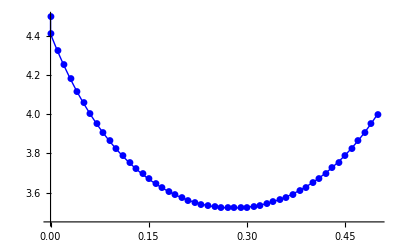

```mathematica
Clear[k,T,Δx,L,i,t]
T=3.;
Δx=.01;
L=.5;
k=.23;
Subscript[u, 0]=4.5;
Subscript[u, L]=4.0;

Subscript[v, 0]=-9.;
Subscript[v, bar]=Subscript[v, 0];

t=0;
While[t<51,
	Subscript[v, t+1]=Subscript[v, t]+Δx*k*(Subscript[u, t]^4-T^4);
	Subscript[u, t+1]=Subscript[u, t]+Δx/2*(Subscript[v, t]+Subscript[v, t+1]);
	Subscript[u, bar]=Subscript[u, t+1];
	t++;	
	];
(*Print["u_bar = ",Subscript[u, bar]];*)

Subscript[v, 0]=Subscript[v, 0]-1.;
Subscript[v, bar2]=Subscript[v, 0];
(*Print["v_bar2 = ",Subscript[v, bar2]];*)
t=0;
While[t<51,
	Subscript[v, t+1]=Subscript[v, t]+Δx*k*(Subscript[u, t]^4-T^4);
	Subscript[u, t+1]=Subscript[u, t]+Δx/2*(Subscript[v, t]+Subscript[v, t+1]);
	t++;
	Subscript[u, bar2]=Subscript[u, t];	
	];
(*Print["u_bar2 = ",Subscript[u, bar2]];*)
Subscript[v, 0]=Subscript[v, bar2]+(4.0-Subscript[u, bar2])*(Subscript[v, bar]-Subscript[v, bar2])/(Subscript[u, bar]-Subscript[u, bar2]);
Subscript[v, α]=Subscript[v, 0];
(*Print["vbar 3 = ",Subscript[v, 0]];*)
t=0;
While[t<51,
	Subscript[v, t+1]=Subscript[v, t]+Δx*k*(Subscript[u, t]^4-T^4);
	Subscript[u, t+1]=Subscript[u, t]+Δx/2*(Subscript[v, t]+Subscript[v, t+1]);
	t++;	
	];
(*Print["u_t = ", Subscript[u, t]];*)
(*now iterate with 2 prior v's*)
While[Abs[Subscript[u, L]-Subscript[u, t]]≥.01,
Subscript[v, α2]=Subscript[v, α]+(4.0-Subscript[u, t])*(Subscript[v, bar2]-Subscript[v, α])/(Subscript[u, bar2]-Subscript[u, t]);
Subscript[u, bar2]=Subscript[u, t];
Print["v_α2 = ",Subscript[v, α2]];
Subscript[v, bar2]=Subscript[v, α];
Subscript[v, α]=Subscript[v, α2];
Subscript[v, 0]=Subscript[v, α2];
t=0;
sArray={{t,Subscript[u, 0]}};
While[t<51,
	Subscript[v, t+1]=Subscript[v, t]+Δx*k*(Subscript[u, t]^4-T^4);
	Subscript[u, t+1]=Subscript[u, t]+Δx/2*(Subscript[v, t]+Subscript[v, t+1]);
	AppendTo[sArray,{t*Δx,Subscript[u, t+1]}];
	t++;	
	];
Print["u_t = ", Subscript[u, t]];
]
fPlot=ListLinePlot[sArray, PlotMarkers->Automatic,PlotStyle->{Blue}];
Print["Final temperature using shooting method and guesses for initial slope at -9.0 and -10.0 = ",Subscript[u, t]]
Show[fPlot]
```